```mathematica
kappa[α_,λ_] := (-1/2(α-1-λ) + 1/2 √((α+1 + λ)^2-4α))
gp[α_,λ_] := α/( α+kappa[α,λ])^2;
Eg[α_,λ_,σ_] := 1/(1-gp[α,λ])(kappa[α,λ]^2/( α+kappa[α,λ])^2+σ gp[α,λ]);
Egd[α_,λ_,σ_] =  D[Eg[α,λ,σ], α];
σ2[λ_,s_]:=3 (1+s) λ (2+3 (1+s) λ-2 √(1+λ+s λ) √(1+9 (1+s) λ) Cos[1/3 (π+ArcTan[-1+9 λ (2+3 λ),8 √λ])]);
```

```mathematica
Analysis of Eg: When Double Descent Occurs?
```

```mathematica
Egd[α,λ,σ]-(((1+α+λ)^2(α+λ-5)+2(1-α+λ) σ+2 (2+λ) (1+3 α+λ))/(2 (-4 α+(α+1+λ)^2)^(3/2))-1/2)//FullSimplify
```

0

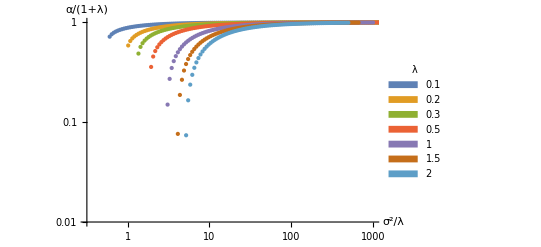

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]
f[λ_,σ_]:=α/(1+λ)/.Refine[Last[NSolve[(1+α+λ)^2(α+λ-5)+2(1-α+λ) σ+2 (2+λ) (1+3 α+λ)==(-4 α+(α+1+λ)^2)^(3/2)&&α>0, α,Reals]],σ>0]
λList = { 0.1, 0.2, 0.3, 0.5,1,1.5,2};
σList = logspace[-2,3,200];
alphastar = Table[f[λ,σ/λ],{λ,λList},{σ,σList}];
TotalList = ConstantArray[0,{Length[λList],Length[σList]}];
Do[TotalList[[i]] = Transpose[{σList/λList[[i]], alphastar[[i]]}],{i, Length[λList]}];
plot=ListLogLogPlot[TotalList,PlotRange->{{10^-0.5,10^3},{10^-2,1}},PlotStyle->PointSize[Medium],Joined->False, PlotLegends->Placed[SwatchLegend[λList,LegendLabel-> "λ",LegendFunction->"Frame"],{0.9,0.5}],AxesLabel->{Style["σ^2/λ",Bold,16],Style["α/(1+λ)",Bold,16]}, AxesStyle->Directive[Black, 12],Ticks->{Table[{10^k,Superscript[10,k]},{k,-2,5}],Table[{10^k,Superscript[10,k]},{k,-2,5}]}]
```

```mathematica
Export["DoubleDescentLocations.pdf", plot, ImageResolution -> 5000]
```

DoubleDescentLocations.pdf